```mathematica
SetOptions[EvaluationNotebook[],PrintPrecision->Round[MachinePrecision]]
```

```mathematica
rawData={{1,
2,
3,
4,
5,
6,
7,
8,
9,
10,
11,
12,
13,
14,
15},
{0,
0.065743,
0.092204,
0.111701,
0.129847,
0.143638,
0.156868,
0.169667,
0.181285,
0.192732,
0.202532,
0.212360,
0.222212,
0.230763,
0.238582}}
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{0,0.065743,0.092204,0.111701,0.129847,0.143638,0.156868,0.169667,0.181285,0.192732,0.202532,0.21236,0.222212,0.230763,0.238582}}

```mathematica
ydata=0.02*(#-1)&/@data[[1]]
xdata=data[[2]]
```

{0.,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2,0.22,0.24,0.26,0.28}

{0,0.065743,0.092204,0.111701,0.129847,0.143638,0.156868,0.169667,0.181285,0.192732,0.202532,0.21236,0.222212,0.230763,0.238582}

```mathematica
{data[[1]],xdata,ydata}//Transpose//TeXForm//CopyToClipboard
```

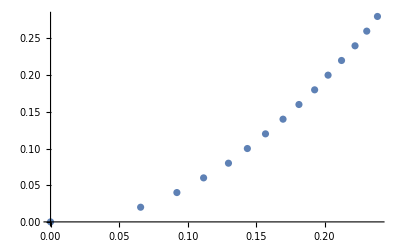

```mathematica
ListPlot[Transpose[{xdata,ydata}]]
```

```mathematica
n=Length[xdata];
sumx=Total[xdata];
sumx2=Total[#^2&/@xdata];
sumx3=Total[#^3&/@xdata];
sumx4=Total[#^4&/@xdata];
sumy=Total[ydata];
sumyx=Sum[ydata[[i]] xdata[[i]],{i,1,n}];
sumyx2=Sum[ydata[[i]]xdata[[i]]^2,{i,1,n}];
```

```mathematica
Δ=Det[({{n, sumx, sumx2}, {sumx, sumx2, sumx3}, {sumx2, sumx3, sumx4}})]
a1=1/Δ Det[({{sumy, sumx, sumx2}, {sumyx, sumx2, sumx3}, {sumyx2, sumx3, sumx4}})]
a2=1/Δ Det[({{n, sumy, sumx2}, {sumx, sumyx, sumx3}, {sumx2, sumyx2, sumx4}})]
a3=1/Δ Det[({{n, sumx, sumy}, {sumx, sumx2, sumyx}, {sumx2, sumx3, sumyx2}})]
```

0.000334195

0.0000189014

-0.0249949

4.998

```mathematica
FindFit[Transpose[{xdata,ydata}], a x^2+ b x + c,{a,b,c},x]
```

{a→4.998,b→-0.0249949,c→0.0000189014}

```mathematica
cross=Graphics[{Line[{{-1,-1},{1,1}}],Line[{{1,-1},{-1,1}}]},ImageSize->11,ImagePadding->1.5]
```

-Graphics-

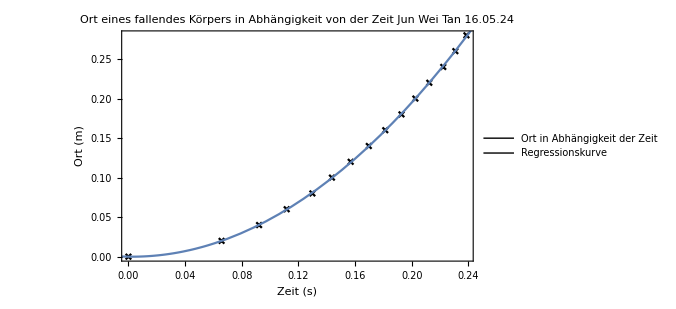

```mathematica
plt=Legended[Show[ListPlot[Transpose[{xdata,ydata}],PlotMarkers->{cross,0.02},PlotStyle->Black],Plot[a1 + a2 x + a3 x^2,{x,Min[xdata]-0.1,Max[xdata]+0.1}],PlotRange->{{Min[xdata],Max[xdata]},{0,Max[ydata]}},Frame->True,Axes->False,FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[15,Black,Opacity[1],FontOpacity[1]],ImageSize->500,PlotLegends->Automatic,FrameLabel->{"Zeit (s)","Ort (m)"},LabelStyle->Directive[Black,15],PlotLabel->"Ort eines fallendes Körpers in Abhängigkeit von der Zeit\n Jun Wei Tan 16.05.24"],Placed[SwatchLegend[{Black,ColorData[97,1]},{TextCell["Ort in Abhängigkeit\n der Zeit"],"Regressionskurve"},LegendMarkers->{cross,Graphics[{Line[{{0,0},{1,0}}]}]}],{Scaled[0.20],Scaled[0.88]}]]
```

```mathematica
Export[NotebookDirectory[]<>"plt.pdf",plt,Background->None]
```

D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Advanced Mistake Counting\plt.pdf

```mathematica
2 a3
```

9.996